# Final Version Of SyntaxCorrector

## Defined functions

#### Syntax Corrector

```mathematica
syntaxCorrector[str_String]:=
Module[
{inp=str,result={},openbrack,closebrack,openbrace,closebrace,openparen,closeparen},
openbrack=StringCount[str,{"["}];
closebrack=StringCount[str,{"]"}];
openbrace=StringCount[str,{"{"}];
closebrace=StringCount[str,{"}"}];
openparen=StringCount[str,{"("}];
closeparen=StringCount[str,{")"}];
Which[
Not[openbrack==closebrack],
If[
openbrack>closebrack,
AppendTo[result,"Closing Bracket Missed"];
(*Close Bracket Inserting*)
s1=Table[StringInsert[str,"]",i],{i,1,StringLength[str]+1}];
(*Selecting the True for SyntaxQ*)
s2=Select[s1,Test&];
AppendTo[result,Column[Flatten[{"Possible solutions",s2}]]];
,
AppendTo[result,"Opening Bracket Missed"];
(*Open Bracket Inserting*)
s1=Table[StringInsert[str,"[",i],{i,1,StringLength[str]}];
(*Selecting the True for SyntaxQ*)
s2=Select[s1,testAnalyser[#]&];
AppendTo[result,Column[Flatten[{"Possible solutions",s2}]]];
];
,
Not[StringCount[str,{"{"}]==StringCount[str,{"}"}]],
If[
openbrace>closebrace,
AppendTo[result,"Closing Braces Missed"];
s1=Table[StringInsert[str,"}",i],{i,1,StringLength[str]+1}];
s2=Select[s1,testAnalyser[#]&];
AppendTo[result,Column[Flatten[{"Possible solutions",s2}]]];
,
AppendTo[result,"Opening Braces Missed"];
s1=Table[StringInsert[str,"{",i],{i,1,StringLength[str]+1}];
s2=Select[s1,testAnalyser[#]&];
AppendTo[result,Column[Flatten[{"Possible solutions",s2}]]];
];
,
Not[StringCount[str,{"("}]==StringCount[str,{")"}]],
If[
openparen>closeparen,
AppendTo[result,"Closing Parenthes Missed"];
s1=Table[StringInsert[str,")",i],{i,1,StringLength[str]+1}];
s2=Select[s1,testAnalyser[#]&];
AppendTo[result,Column[Flatten[{"Possible solutions",s2}]]];
,
AppendTo[result,"Opening Parenthes Missed"];
s1=Table[StringInsert[str,"(",i],{i,1,StringLength[str]+1}];
s2=Select[s1,testAnalyser[#]&];
AppendTo[result,Column[Flatten[{"Possible solutions",s2}]]];
];
,
Not[EvenQ[StringCount[str,"\""]]],
AppendTo[result,"Quotes Missed"];
s1=Table[StringInsert[str,"\"",i],{i,1,StringLength[str]+1}];
s2=Select[s1,testAnalyser[#]&];
AppendTo[result,Column[Flatten[{"Possible solutions",s2}]]];
,
StringCount[str,{"["}]==StringCount[str,{"]"}]&&
StringCount[str,{"{"}]==StringCount[str,{"}"}]&&
StringCount[str,{"("}]==StringCount[str,{")"}]&&
StringCount[str,{"("}]==StringCount[str,{")"}]&&
EvenQ[StringCount[str,"\""]],
AppendTo[result,"Letter or Number Missed"];
s1=Table[StringInsert[str,"a",i],{i,1,StringLength[str]+1}];
s2=Select[s1,testAnalyser[#]&];
AppendTo[result,Column[Flatten[{"Possible solutions",s2}]]];
];
Column[result]
]
```

#### Message Analyzer

```mathematica
messageAnalysis[str_]:=
Module[{mess,s=str,res,result},
Block[{$MessageList={}},
Quiet[
res=ToExpression[str];
mess=$MessageList;
];
If[mess=!={},result=False,result=True];
];
result
];
```

#### Test

```mathematica
testAnalyser[str_String]:=messageAnalysis[str]&&EditDistance[StringDelete[ToString[ToExpression[str],InputForm],WhitespaceCharacter],str]>1
```

## Examples

```mathematica
syntaxCorrector["N[N[Nest[Nest[x^2,x,6,4,3]]]"]
```

Closing Bracket Missed
Possible solutions
N[N[Nest[Nest[x^2,x,6],4,3]]]

```mathematica
syntaxCorrector["Fold[f[][],x[[][],{1,2,3}]"]
```

Closing Bracket Missed
Possible solutions
Fold[f[][],x[][][],{1,2,3}]
Fold[f[][],x[[]][],{1,2,3}]
Fold[f[][],x[[]][],{1,2,3}]

```mathematica
syntaxCorrector["Fold[f[][,x[],{1,2,3}]"]
```

Closing Bracket Missed
Possible solutions
Fold[f[][],x[],{1,2,3}]
Fold[f[][,]x[],{1,2,3}]
Fold[f[][,x][],{1,2,3}]
Fold[f[][,x[]],{1,2,3}]
Fold[f[][,x[]],{1,2,3}]
Fold[f[][,x[],]{1,2,3}]
Fold[f[][,x[],{1,2,3}]]
Fold[f[][,x[],{1,2,3}]]

```mathematica
syntaxCorrector["Fold[f[][,x[],{1,2,3}]"]
```

Closing Bracket Missed
Possible solutions
Fold[f[][],x[],{1,2,3}]
Fold[f[][,]x[],{1,2,3}]
Fold[f[][,x][],{1,2,3}]
Fold[f[][,x[]],{1,2,3}]
Fold[f[][,x[]],{1,2,3}]
Fold[f[][,x[],]{1,2,3}]
Fold[f[][,x[],{1,2,3}]]
Fold[f[][,x[],{1,2,3}]]

```mathematica
syntaxCorrector["Fold[f[][][],x[][[],{1,2,3}]"]
```

Closing Bracket Missed
Possible solutions
Fold[f[][][],x[][][],{1,2,3}]
Fold[f[][][],x[][[]],{1,2,3}]
Fold[f[][][],x[][[]],{1,2,3}]

```mathematica
syntaxCorrector["Fold[f,x[,{1,2,3}]"]
```

Closing Bracket Missed
Possible solutions
Fold[f,x[],{1,2,3}]
Fold[f,x[,]{1,2,3}]
Fold[f,x[,{1,2,3}]]
Fold[f,x[,{1,2,3}]]

```mathematica
ToExpression["Function[x,Evaluate[Together[Nest[Function[z,](z+a/z)/2,x,4]]]]"]
```

Function[x,(1/2 (a/z+z) Function[z,Null])[(1/2 (a/z+z) Function[z,Null])[(1/2 (a/z+z) Function[z,Null])[(1/2 (a/z+z) Function[z,Null])[x]]]]]

```mathematica
syntaxCorrector["Function[x,Evaluate[Together[Nest[Function[z,(z+a/z)/2,x,4]]]]"]
```

Closing Bracket Missed
Possible solutions
Function[x,Evaluate[Together[Nest[Function[z,](z+a/z)/2,x,4]]]]
Function[x,Evaluate[Together[Nest[Function[z,(z+a/z)]/2,x,4]]]]
Function[x,Evaluate[Together[Nest[Function[z,(z+a/z)/2],x,4]]]]

```mathematica
syntaxCorrector@"Nest[f,,4]"
```

Letter or Number Missed
Possible solutions
aNest[f,,4]
Naest[f,,4]
Neast[f,,4]
Nesat[f,,4]
Nesta[f,,4]
Nest[af,,4]
Nest[fa,,4]
Nest[f,a,4]
Nest[f,,4]a

## DataSets for NeuralNetwork

#### trainingSet construction

```mathematica
trainingSet[str_String]:=Flatten[Table[{StringDrop[str,{i}]->str},{i,1,StringLength[str]}]];
trainingCheck[str_String]:=Table[StringDrop[str,{i}],{i,1,StringLength[str]}];
```

```mathematica
trainingSet2[str_String]:=Flatten[Table[{StringPartition[StringDrop[str,{i}],1]->StringPartition[str,1]},{i,1,StringLength[str]}]];
```

```mathematica
trainingSet3[str_String]:=Table[{StringDrop[str,{i}],str},{i,1,StringLength[str]}];
```

```mathematica
trainingSet4[str_String]:=Flatten[Table[{ToCharacterCode[StringDrop[str,{i}]]->ToCharacterCode[str]},{i,1,StringLength[str]}]];
```

```mathematica
trainingSet5[str_String]:=Flatten[Table[{ToCharacterCode[StringReplacePart[str," ",{i,i}]]->ToCharacterCode[str]},{i,1,StringLength[str]}]];
```

```mathematica
trainingValid5[str_String]:=Flatten[Table[{ToCharacterCode[StringReplacePart[str," ",{i,i}]]->ToCharacterCode[str]},{i,1,StringLength[str]}]];
```

```mathematica
trainingSet6[str_String]:=Flatten[Table[{ToCharacterCode[StringReplacePart[str,FromCharacterCode[j],{i,i}]]->ToCharacterCode[str]},{i,1,StringLength[str]},{j,49,122}]];
```

```mathematica
FromCharacterCode[#]&/@Range[49,122]
```

{1,2,3,4,5,6,7,8,9,:,;,<,=,>,?,@,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,[,\,],^,_,`,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
trainingSet5["kk"]
```

{{32,107}→{107,107},{107,32}→{107,107}}

```mathematica
StringReplacePart
```

#### Construction of training set

```mathematica
NotebookImport
```

```mathematica
NotebookImport[FileNameJoin[{$InstallationDirectory,"Documentation","English","System","ReferencePages","Symbols",#<>".nb"}],"Input"->"InputText"]&/@Names["System`*"][[3000;;3009]]
```

{{LessLess[x, y, z]},{LessSlantEqual[1, 2]},{LessThan[4][2],LessThan[y][x],Select[{0, 5, 10, 15}, LessThan[10]],LessThan[10][6],LessThan[Quantity[1, "Hour"]][Quantity[50, "Minutes"]],LessThan[Today][Yesterday],LessThan[DateObject[{2015, 8, 1}, "Day", "Gregorian", -6.`]][\r
 DateObject[{2015, 6, 1}, "Day", "Gregorian", -6.`]],LessThan[5][x],LessThan[x][5],EntityValue[\r
 EntityClass[\r
  "Country", {"Area" → \r
    LessThan[Quantity[100, "Kilometers"^2]]}], "Entities"],EntityValue[\r
 EntityClass[\r
  "Country", {"Area" → \r
    LessThan[Quantity[100, "Kilometers"^2]]}], "Population"],Total[%],EntityValue[\r
 Entity["Country", {"Area" → \r
    LessThan[Quantity[100, "Kilometers"^2]]}], "Population"],Select[{0, 5, 10, 15}, Less[#, 10] &],Select[{0, 5, 10, 15}, LessThan[10]],Select[LessThan[10]][{0, 5, 10, 15}]},{LessTilde[x, y, z]},{StringMatchQ[#, LetterCharacter] & /@ {"a", "1", "B", ".", " "},StringMatchQ["abcdefg", LetterCharacter ..],StringMatchQ["abdc12", LetterCharacter ..],StringMatchQ[#, LetterCharacter] & /@ {"a", "1", "B", " "},LetterQ[#] & /@ {"a", "1", "B", " "}},{LetterCounts["aaaaaaaaaa"],LetterCounts["banana"],LetterCounts["12345"],LetterCounts["YT-1300"],LetterCounts["ab12cd34ef45", 2],LetterCounts["12345", 1, {"1", "5"}],LetterCounts["TK-421", 1, {"1", "2"}],LetterCounts["Alabama", IgnoreCase → False],LetterCounts["Alabama", IgnoreCase → True],LetterCounts["abABabABabABabABabAB", 2, IgnoreCase → True],LetterCounts["abABabABabABabABabAB", 2, IgnoreCase → False],Take[LetterCounts[WikipediaData["volcano"]], 20],Take[LetterCounts[WikipediaData["volcano"], 3], 20]},{LetterNumber["d"],LetterNumber["D"],LetterNumber["γ", "Greek"],LetterNumber["я", Entity["Language", "Russian"]],LetterNumber[Characters["Turtle"]],Alphabet["Greek"],LetterNumber["λ", "Greek"],Position[Alphabet["Greek"], "λ"],LetterNumber["c"],FromLetterNumber[%],LetterNumber["a", "French"],ToCharacterCode["a"],LetterNumber["α"],LetterNumber[α]},{LetterQ["a"],LetterQ["2"],LetterQ["abcdABCD"],LetterQ["two words"],LetterQ["äé"],LetterQ["𝔄𝔅ℭ𝔇𝔈"],LetterQ["αβγδϵζηθ"],"∑",LetterQ[%],Style[StringJoin[\r
  Select[Characters[FromCharacterCode[Range[1072, 1103]]], \r
   LetterQ]], 14],Style[StringJoin[\r
  Select[Characters[FromCharacterCode[Range[2693, 2787]]], \r
   LetterQ]], 14],Style[StringJoin[\r
  Select[Characters[FromCharacterCode[Range[2821, 2915]]], \r
   LetterQ]], 14],Style[StringJoin[\r
  Select[Characters[FromCharacterCode[Range[3329, 3455]]], \r
   LetterQ]], 14],Style[StringJoin[\r
  Select[Characters[FromCharacterCode[Range[11648, 11742]]], \r
   LetterQ]], 14],\r
BoxData[\r
RowBox[{"Style", "[", \r
RowBox[{\r
RowBox[{"StringJoin", "[", \r
RowBox[{"Select", "[", \r
RowBox[{\r
RowBox[{"Characters", "[", \r
RowBox[{"FromCharacterCode", "[", \r
RowBox[{"Range", "[", \r
RowBox[{"12353", ",", "12436"}], "]"}], "]"}], "]"}], ",", \r
           "LetterQ"}], "]"}], "]"}], ",", "14"}], "]"}]],Style[StringJoin[\r
  Select[Characters[FromCharacterCode[Range[12449, 12538]]], \r
   LetterQ]], 14],Style[StringJoin[\r
  Select[Characters[FromCharacterCode[Range[2^16 - 1]]], \r
   LetterQ]], 14],CharacterRange["𝒜", "𝒢"],LetterQ /@ %,LetterQ["ℬ"],ListPlot[Flatten[\r
  ToCharacterCode[\r
   Select[Characters[FromCharacterCode[Range[2^16 - 1]]], LetterQ]]]],With[{u = \r
   Select[Characters[FromCharacterCode[Range[1, 2000, 5]]], LetterQ]},\r
  ListPlot[MapIndexed[{{First[#2], First[ToCharacterCode[#1]]}} &, u],\r
   PlotMarkers -> u, Frame -> True]]},{Level[a + f[x, y^n], {-1}],Level[a + f[x, y^n], 2],Level[a + f[x, y^n], {0, Infinity}],Level[<|1 → a, 2 → b|>, -1],Level[<|1 → a, 2 → b|>, {1}],Level[<|1 → <|a → b, c → d|>|>, {2}],Level[<|1 → <|a → b, c → d|>|>, {1, 2}],Level[{{{{a}}}}, 1],Level[{{{{a}}}}, 2],Level[{{{{a}}}}, 3],Level[{{{{a}}}}, 4],Level[{{{{a}}}}, 5],Level[{{{{a}}}}, -1],Level[{{{{a}}}}, -2],Level[{{{{a}}}}, -3],Level[{{{{a}}}}, -4],Level[{{{{a}}}}, -5],Level[{{{{a}}}}, {2, 3}],Level[{{{{a}}}}, {0, -1}],Level[h0[h1[h2[h3[a]]]], {0, -1}],Level[{{{{a}}}}, 3, Heads -> True],Level[x^2 + y^3, 3, Heads -> True],Integrate[Sin[Tan[x]], x],Level[%, {-1}],Level[Integrate[Sin[Tan[x]], x], {-1}, Heads -> True],Union[Level[Integrate[Sin[Tan[x]], x], {-1}, Heads -> True]],Array[a, {2, 2, 2}],Level[%, {3}],Level[h1[h2[h3[x]]], -1],Level[h1[h2[h3[x]]], {0, -1}]},{data = RandomVariate[NormalDistribution[], {2, 100}];,LeveneTest[data],ℋ = LeveneTest[data, Automatic, "HypothesisTestData"],ℋ["Properties"],data = RandomVariate[NormalDistribution[1, 2.1], 10^3];,LeveneTest[data, 4, "TestDataTable"],Variance[data],LeveneTest[data, 4, "TestDataTable", \r
 AlternativeHypothesis → "Greater"],SeedRandom[3];,data1 = RandomVariate[NormalDistribution[], 500];,LeveneTest[data1],sample = Table[\r
   Quiet@LeveneTest[\r
     RandomVariate[NormalDistribution[0, 1], 100]], {10^3}];,Histogram[sample, Automatic, PDF],SeedRandom[3];,data2 = RandomVariate[NormalDistribution[1, 3], 500];,LeveneTest[data2],SeedRandom[3];,data1 = RandomVariate[NormalDistribution[0, 2], 10^4];\r
data2 = RandomVariate[NormalDistribution[0, 2.1], 10^4];,LeveneTest[data1, 2^2],LeveneTest[data2, 2^2],SeedRandom[3];,data1 = RandomVariate[NormalDistribution[0, 3], 500];\r
data2 = RandomVariate[NormalDistribution[1, 3], 500];,LeveneTest[{data1, data2}],sample = Table[\r
   Quiet@LeveneTest[{RandomVariate[NormalDistribution[0, 3], 100], \r
      RandomVariate[NormalDistribution[1, 3], 100]}], {5 10^3}];,Histogram[sample, Automatic, PDF],SeedRandom[3];,data3 = RandomVariate[NormalDistribution[10, 1], 350];,LeveneTest[{data1, data3}],SeedRandom[3];,data1 = RandomVariate[NormalDistribution[0, 2], 500];\r
data2 = RandomVariate[NormalDistribution[0, 1], 500];,Subscript[σ, 0] = 4;,LeveneTest[{data1, data2}, Subscript[σ, 0]],LeveneTest[{data2, data1}, 1/Subscript[σ, 0]],LeveneTest[{data2, data1}, Subscript[σ, 0]],SeedRandom[3];,data1 = RandomVariate[NormalDistribution[10, 1], 500];\r
data2 = RandomVariate[NormalDistribution[0, 1], 200];\r
data3 = RandomVariate[NormalDistribution[-3, 1], 400];,LeveneTest[{data1, data2, data3}],SeedRandom[3];,data = RandomVariate[NormalDistribution[], {2, 10^4}];,ℋ = LeveneTest[data, 1, "HypothesisTestData"];,ℋ["Properties"],SeedRandom[3];,data = Table[\r
   RandomVariate[NormalDistribution[0, 1], \r
    i], {i, {1000, 2000, 3000}}];,ℋ = LeveneTest[data, 1, "HypothesisTestData"];,ℋ["PValue"],ℋ["TestStatistic"],ℋ["DegreesOfFreedom"],SeedRandom[3];,data = RandomVariate[NormalDistribution[], {2, 100}];,ℋ = LeveneTest[data, 1, "HypothesisTestData"];,ℋ["PValue", "TestStatistic", "DegreesOfFreedom"],SeedRandom[3];,data = RandomVariate[NormalDistribution[], {2, 10^3}];,ℋ = LeveneTest[data, 1, "HypothesisTestData"];,ℋ["TestDataTable"],ℋ["TestData"],SeedRandom[3];,data = RandomVariate[NormalDistribution[], {3, 10^4}];,ℋ = LeveneTest[data, 1, "HypothesisTestData"];,ℋ["PValueTable"],ℋ["PValue"],ℋ["TestStatisticTable"],ℋ["TestStatistic"],data = RandomVariate[NormalDistribution[], 100];,LeveneTest[data, 1, AlternativeHypothesis → "Unequal"],LeveneTest[data, 1, AlternativeHypothesis → Automatic],data = RandomVariate[NormalDistribution[0, 1.25], 100];,LeveneTest[data, Automatic, AlternativeHypothesis → "Unequal"],LeveneTest[data, Automatic, AlternativeHypothesis → "Less"],LeveneTest[data, Automatic, AlternativeHypothesis → "Greater"],data1 = RandomVariate[NormalDistribution[0, .9], 100];\r
data2 = RandomVariate[NormalDistribution[0, 1], 100];,Variance[data1]/Variance[data2],LeveneTest[{data1, data2}, 1, AlternativeHypothesis → "Less"],LeveneTest[{data1, data2}, 1.5, AlternativeHypothesis → "Less"],data = BlockRandom[SeedRandom[5]; \r
   RandomVariate[StudentTDistribution[3], 50]];,LeveneTest[data, 1, SignificanceLevel → .005],LeveneTest[data, 1, SignificanceLevel → Automatic],data = BlockRandom[SeedRandom[1]; \r
   RandomVariate[NormalDistribution[0, 1], 100]];,ℋ1 = LeveneTest[data, 1.5, "HypothesisTestData", \r
   SignificanceLevel → .05];,ℋ2 = LeveneTest[data, 1.5, "HypothesisTestData", \r
   SignificanceLevel → .01];,ℋ1["TestConclusion"] // TraditionalForm,ℋ2["TestConclusion"] // TraditionalForm,ℋ1["ShortTestConclusion"],ℋ2["ShortTestConclusion"],data1 = RandomVariate[StudentTDistribution[3], 1000];\r
data2 = RandomVariate[NormalDistribution[0, Sqrt[3]], 1000];,LeveneTest[{data1, data2}, 1/4, VerifyTestAssumptions → All],LeveneTest[{data1, data2}, 1/4, VerifyTestAssumptions → None],data1 = RandomVariate[StudentTDistribution[3], 1000];\r
data2 = RandomVariate[NormalDistribution[0, Sqrt[3]], 1000];,LeveneTest[{data1, data2}, 1/4, VerifyTestAssumptions → "Normality"],LeveneTest[{data1, data2}, 1/4, \r
 VerifyTestAssumptions → "Normality" → True],data = RandomVariate[NormalDistribution[], {1000, 100}];,AbsoluteTiming[\r
 T = Quiet@LeveneTest[#, Automatic, "TestStatistic"] & /@ data;],AbsoluteTiming[\r
 T2 = Quiet@\r
      LeveneTest[#, Automatic, "TestStatistic", \r
       VerifyTestAssumptions → None] & /@ data;],SmoothHistogram[{T, T2}],HomogeneityOfVarianceTest[data_] := \r
 With[{nh = Ceiling[Length[data]/2]}, \r
  LeveneTest[TakeDrop[data, nh], 1, "TestDataTable", \r
   VerifyTestAssumptions → None]],data = ({#1⟦1⟧, #1⟦2⟧, #1⟦3⟧, \r
      1.2 + (3.7 + RandomReal[{-1, 1}]) #1⟦1⟧ - 2 #1⟦2⟧ + \r
       23.4 #1⟦3⟧} &) /@ RandomReal[10, {100, 3}];,lm = LinearModelFit[data, {x, y, z}, {x, y, z}];,Row[Table[\r
  ListPlot[Transpose[{data⟦All, i⟧, lm["FitResiduals"]}], \r
   Frame → True, FrameLabel → {{x, y, z}⟦i⟧, "Residual"}], {i, 3}]],res = (SortBy[#1, First]⟦All, 2⟧ &) /@ \r
   Table[Transpose[{data⟦All, i⟧, lm["FitResiduals"]}], {i, 3}];,HomogeneityOfVarianceTest /@ res,SeedRandom[3];,data = RandomVariate[NormalDistribution[], 100];,LeveneTest[data],FisherRatioTest[data],SeedRandom[3];,data = RandomVariate[NormalDistribution[], {1000, 100}];,T = LeveneTest[#, Automatic, "TestStatistic", \r
     VerifyTestAssumptions → None] & /@ data;,Show[SmoothHistogram[T, PlotStyle → Orange], \r
 Plot[PDF[ChiSquareDistribution[99], x], {x, 50, 160}], \r
 PlotRange → All],EstimatedDistribution[T, ChiSquareDistribution[df]],DistributionFitTest[T, ChiSquareDistribution[99]],n = 100;\r
m = 75;\r
SeedRandom[3];\r
data1 = RandomVariate[NormalDistribution[], {1000, n}];\r
data2 = RandomVariate[NormalDistribution[], {1000, m}];,T = MapThread[\r
   LeveneTest[{#1, #2}, Automatic, "TestStatistic", \r
     VerifyTestAssumptions → None] &, {data1, data2}];,Show[Histogram[T, {0.2}, "PDF"], \r
 Plot[PDF[FRatioDistribution[1, n + m - 2], x], {x, 0, 8}, \r
  PlotRange → {0, 1.5}]],DistributionFitTest[T, \r
 FRatioDistribution[1, n + m - 2], "TestConclusion"],SeedRandom[3];,data1 = RandomVariate[LaplaceDistribution[1, 2], {1000, 100}];\r
data2 = RandomVariate[LaplaceDistribution[1, 2], {1000, 75}];,fisher = MapThread[\r
   FisherRatioTest[{#1, #2}, VerifyTestAssumptions → None] &, {data1, \r
    data2}];,levene = MapThread[\r
   LeveneTest[{#1, #2}, VerifyTestAssumptions → None] &, {data1, \r
    data2}];,Histogram[{fisher, levene}, Automatic, "PDF"],Subscript[n, 1] = 100; Subscript[n, 2] = 75; Subscript[σ, 0] = 2;,SeedRandom[3];,data1 = RandomVariate[NormalDistribution[0, Subscript[σ, 0]], \r
   Subscript[n, 1]];\r
data2 = RandomVariate[NormalDistribution[0, 1], Subscript[n, 2]];,Subscript[n, t] = Subscript[n, 1] + Subscript[n, 2];,levene[d1_, d2_] := Block[{μZ1, μZ2, z1, z2, μZZ},\r
  z1 = Abs[Standardize[d1, Mean, 1 &]];\r
  z2 = Subscript[σ, 0] Abs[Standardize[d2, Mean, 1 &]];\r
  μZ1 = Mean[z1]; μZ2 = Mean[z2];\r
  μZZ = (Subscript[n, 1] μZ1 + Subscript[n, 2] μZ2)/Subscript[n, t];\r
  (Subscript[n, t] - 2) (\r
   Subscript[n, 1] (μZ1 - μZZ)^2 + \r
    Subscript[n, \r
     2] (μZ2 - μZZ)^2)/((z1 - μZ1).(z1 - μZ1) + (z2 - μZ2).(z2 - μZ2))\r
  ],levene[data1, data2],LeveneTest[{data1, data2}, Subscript[σ, 0]^2, "TestStatistic"],Subscript[n, 1] = 100; Subscript[n, 2] = 75; Subscript[n, 3] = 150;,SeedRandom[3];,data1 = RandomVariate[NormalDistribution[-4, 3], Subscript[n, 1]];\r
data2 = RandomVariate[NormalDistribution[1, 3], Subscript[n, 2]];\r
data3 = RandomVariate[NormalDistribution[5, 3], Subscript[n, 3]];,Subscript[n, t] = Subscript[n, 1] + Subscript[n, 2] + Subscript[n, 3];,levene3[d1_, d2_, d3_] := Block[{μZ1, μZ2, μZ3, z1, z2, z3, μZZ},\r
  z1 = Abs[d1 - Mean[d1]];\r
  z2 = Abs[d2 - Mean[d2]];\r
  z3 = Abs[d3 - Mean[d3]];\r
  μZ1 = Mean[z1]; μZ2 = Mean[z2]; μZ3 = Mean[z3];\r
  μZZ = (Subscript[n, 1] μZ1 + Subscript[n, 2] μZ2 + \r
    Subscript[n, 3] μZ3)/Subscript[n, t];\r
  (Subscript[n, t] - 3)/2 (\r
   Subscript[n, 1] (μZ1 - μZZ)^2 + Subscript[n, 2] (μZ2 - μZZ)^2 + \r
    Subscript[n, 3] (μZ3 - μZZ)^2)/(\r
   Total[(z1 - μZ1)^2] + Total[(z2 - μZ2)^2] + Total[(z3 - μZ3)^2])\r
  ],levene3[data1, data2, data3],LeveneTest[{data1, data2, data3}, 1, "TestStatistic"],ts = TemporalData[TimeSeries, {CompressedData["\r
1:eJwBOQPG/CFib1JlAgAAAAEAAABlAAAA/PYqxN+X8z+3X5GhyqzeP5CuGSVs\r
COU/6gW3Q9ODyz8UoDPB1lvnP2gtJOf678+/fg8X7itC9b+ifaVg7K/hP7Cb\r
PvIVq8g/8VzLfwbl8j9xv1++fqzyv/ogumfvLOc/2lH/DYsE+T/snMgxQUT5\r
P9/vcvl0N9I/ZVpzOut45b+sSWmvNKr/v6C86n7l+PM/BAzAnUQF7T+Fqh1s\r
klDzv9yUjaoGwte/41o52nyk9L+ZSKZCVRkFwEdAlZ8HrP2/JoZVOtXo17+y\r
FeEX9rrKP5nG9i58Vr2/UzT02hTHAMBekGiCnJ3Vv8FUfITGtOS/11bF8H81\r
9L8y33C+4Rvfv1Hx6g0fU+6/1o7s2IQi4D+kmplJf+P3P4025NI5ONY/l1kK\r
MU8BAkAW26+8OGXqP16doWiVPeQ/L9akxry90L8hDSyLQALfP8UG4Pc349I/\r
enHoUMJmpT+QpZzYePPMv73mvJYmMMc/bixiaHru+D+wWmt9r37QPy6dWHWS\r
lNq/BpHOWLlK07+EsjkVUSj6P5hjJUE0LPC/CvElnlMG9j/XkSE4Jd34P4ZK\r
7oH8KNy/ssEspu6I0L+U6Qfx0lfyv4w/XIYCNNS/z6B++aSqyz8ulQXeVWjn\r
PxlgbFUeEu6/22dM/8dh1D9fHJO/U7zev8pzJ0XQH9Y/lPIKHHp65L/s0V0p\r
OjGsPy/37+vQAOA/gYS95GCB4j+BELaE81XiP0QWnKlv5JU/M8GIybwR0z+u\r
L9uIFnzKvwKmgTH1mPG/J3NbAqTZBkDcL6wweakJQFgP8najD8u/GibcudpJ\r
q7/QdeEyH8PEv+DU8Hynouu/hMi7njOl3L/5TIUW9hPTv7pS6rslndc/bOqN\r
XWplAkCgvOdNarG/v9qFnOEhXdQ/3zQlbLj7zT+pSIyzS9ikP3OnpBVj9vE/\r
o+ll8qcvAMC4ppB+3Mr2v4nBE1WPZfa/b4TEMXSYBcBIu++/BeXgv2Xqvs/S\r
TOg/wC/sPBqKnL8ABU+u66/iv65b2Y+eLdm/3Ve3tZvW8D/o8ybMdeftP5zA\r
CZ4Iqtg/ns7gYZsk379CUsbj/sjmvyBzvkY=\r
"], {{0, 100, 1}}, 1, {"Continuous", 1}, {"Discrete", 1}, 1, {\r
    ValueDimensions -> 1, ResamplingMethod -> None}}, False, 10.1];,LeveneTest[ts],LeveneTest[ts["Values"]],td = TemporalData[Automatic, {CompressedData["\r
1:eJwVwws8FIYfAPDzbl6JafJoXun4zPpbVl79f+hIDGcey/5NpZRX8xpdRF7N\r
P/2V1GxKdWjbf0oYuRr5oUuX/9XhrOMcx53jOIe7444P6b99P5+vTWzKl3Hq\r
BALh73F/vb3DJ9jIuR9t7bxX45TTyDxKOK6+uYn5XObnCcE5kEfNmC+b4CDp\r
fNtI3nURWFwxrnE6LQF17Zaqvh8WwHRdo7jHcx2M1ILJ2nXvoHaHcDs9kAX7\r
/uN+rMRDjOsxjZ6VHkNoePjIdJUaF6Isb6hZzc3h7schdXezZUgl2H/anqjE\r
eK57V9o3K+DyjCL3slfAqrEt64W9EsxcD7jUewrgpYEVr3j7JDiHFzoef8+D\r
WMeVnJM2wzjir4rV3auEZv/cQec8IaTmJBskMReg97DN5p0JHjRl8124wjk8\r
1V02tnxlDGvfFX47XNAM2d9TQprqOzGHkX22CKX4W7X3F696+ZDTqVbt59MM\r
i+i/VtHJxc/oZEnKwzewdMnMOs84FQ09nMRtkWsQE91v/35dBfHpWv2xcVNQ\r
bR2QMc5mI5MlvEjO5IAzOVF3oEeIv1wy+q7mtAAuM/oL1R+owDxKZZi0iwti\r
u4OmapnDsO1XCdx8rIDywKi03sxpiKrYaUyrZGOK4BO3jbeLyChXv17YKoJv\r
99EWnS1mkXLyROT2G0s40VU2br5LhkZtqiNRD8XQ5FNdlVeowCDVPbOFF3+i\r
6vdHtxuWeNDgpKX/YkaI9KCqmef/4mOp6ESYz73fUXs9I2oyF+Go9Df7wQI5\r
5vkkP4geWkEqn1RccWYM3+Vn0Tepat7CeW02pU/de9Z1V0DtlmUQRNgKc4yF\r
mGdurn7x5gB6ZXnpyorUvekFwcNfkbvh5tWwtAj+c9QP/9BiQGMYLaUk2OJF\r
R6sTurMyggDO6J356fNLLCSxwkOJWc1wgJN1PEMkwazw6w3B9WpdVZ1ntaRa\r
AvB60HH8wvl2oOu332reXAfS7hb/0Pe9sGH1z2j2y1m0i3vb/5OWCqkkWgch\r
aB6t7nJ/OWTNxVB6W2lF7jJ4TGsYLt3gAu5l+XiuypBEmM0qrmhHd1thxZZj\r
BG9a55ZaZo8KAlj/mDJLb0Td5unSqIg+LKuhNkk6ljGsxV/m3zGFElJ0vonH\r
DApmmIupk5pdPJvggP1PNbpCGJxGh9IN3B/z0Qcx63wcqom2FAbJoO+/el5Z\r
IhZys6qOlSS2A0VBrLlPXgD//D1UgzEh7DTdF3NrhgfQsJxquo2BI9sC61ey\r
l4FsJJsJTH2Kh1u8/NO/r8V4whwzYb8IshSmtA27CdjfaPSQ9UwBy3HJ/x6d\r
WIG+qRA32jkxBJL1B7uTJsBbKs3IGJiCtEPXfPeoD6FOYwRHWKVE01uvRg87\r
yoEW8uPc7rweaHHSeUNgNkPIGSvBrQt8WGo1NtA9KMamcHKSePAuftdJO0TJ\r
nEXjCXbb8NoCUl6Kiv6nVQePchlO0zoy2PvsepDOqQ0ssSaZ+G1odHk47yos\r
vjQGW/OTmoOeSLEnwcw2lsjGlfDO1g/itLoWzw1GvteUImOjYDdIpxCD/Tb+\r
9BKh0HImrG5Nhmh6/ip3fhNv+Fxuzl0WoEg7rFgzkIGRvTP1I6QNeKuz3SmF\r
8wraEq+xlQFKLM39ssES55D4UbpEPinBUFers37jg0ChVZdXlvdgfuonB0n9\r
S8hQSuZtNGah9decpgNXp5Gap80RD6ThgEPj1lB9ESZXrHyT2vozWkR8HaMT\r
tA7FKyNp9n7j2B3jsiC8OIHUE/M069VhfKW7lr7DV8+b/nXvbYFQDorReu1C\r
z0Ugskl/GOzkY5HyxcSkxSjY2p/T0uDIYT5G0yRlKxNJvKeP42xloLln3c23\r
UgVljXevJR9UQA+xIW1b/BoWEs3bTyey4Inzx7UFCS/xSWw+Q3xZDqcu1t6v\r
eT0NzPhV1s6cAeQEtOzxmGYjW+9yws8PpyAmV+l259kI9E2mN5hx7oOZ8Ku1\r
K4ox4BFJfBPfZRj17dPT2DuGjic/fC6NVgDjNM212uUd9LAT7erMx8HB887J\r
N64zQOW/fkphKtDB9JGJQ6oE6kpIS+6zk+j8JN19jSLHSrdYsksRD4mfXfAZ\r
KqFjx72kSMebcmwyPN9xtFwO7KDMI6uPZBB87IKmVacMvnDMf01s68b/A/Gh\r
XVM=\r
"], {{0, 100, 1}}, 2, {"Continuous", 2}, {"Discrete", 1}, 1, {\r
    ValueDimensions -> 1, ResamplingMethod -> None}}, False, 10.1];,LeveneTest[td],data = td["ValueList"] // Flatten;\r
LeveneTest[data],{data1, data2} = td["ValueList"];,LeveneTest[{data1, data2}],data = RandomVariate[LaplaceDistribution[1, 2], {2, 100}];,LeveneTest[data, 1, "TestDataTable"],ConoverTest[data, 1, "TestDataTable"],SiegelTukeyTest[data, 1, "TestDataTable"],data = RandomVariate[NormalDistribution[1, 2], {4, 100}];,Length[data],LeveneTest[data, 2, "TestDataTable"],data = RandomVariate[NormalDistribution[1, 2], {4, 100}];,LeveneTest[data, 1, AlternativeHypothesis → "Unequal"],LeveneTest[data, 1, AlternativeHypothesis → "Greater"],LeveneTest[data, 1, AlternativeHypothesis → "Less"],data = RandomVariate[NormalDistribution[], {250, 100}];,T1 = LeveneTest[#, 1, "TestStatistic", \r
     VerifyTestAssumptions → None] & /@ data;,T2 = LeveneTest[#, 3, "TestStatistic", \r
     VerifyTestAssumptions → None] & /@ data;,SmoothHistogram[{T1, T2}, Filling → Axis, \r
 PlotLegends \r
  → {"H_0 is True", \r
   "H_0 is False"}]}}

```mathematica
NotebookImport[FileNameJoin[{$InstallationDirectory,"Documentation","English","System","ReferencePages","Symbols","Subsets.nb"}],"Input"->"InputText"]
```

{Subsets[{a, b, c}],Subsets[{a, b, c, d}, 2],Subsets[{a, b, c, d}, {2}],Subsets[{a, b, c, d, e}, {3}, 5],Subsets[{a, b, c, d, e}, {0, 5, 2}],Subsets[Range[20], All, {69381}],Subsets[{a, b, c, d}],Subsets[{a, b, c, d}, All, {15, 1, -2}],Subsets[f[a, b, c]],Subsets[a + b + c],Subsets[{1, 2, 3, 4}, {3}],Binomial[4, 3],Graphics[Line[\r
  Subsets[Table[{Cos[2 Pi i/8], Sin[2 Pi i/8]}, {i, 8}], {2}]]],Total[Subsets[Times[a, b, c, d, e], {3}]],Subsets[Divisors[10]],Subsets[{1, 2, 4, 8, 16}, {3}],Total /@ %,Graphics3D[Line /@ Subsets[RandomReal[100, {20, 3}], {2}]],Graphics3D[Line[Subsets[Tuples[{1, 0}, 3], {2}]]],Subsets[{c, b, a}],Subsets[{a, b, b, b}],Tuples[{a, b, c}, 2],Subsets[{a, b, c}, {2}],Subsets[Range[4], All, 8],Take[Subsets[Range[4], All], 8],Subsets[Range[3], All, 10],Off[Subsets::take],Subsets[Range[3], All, 10],Graphics[{Opacity[0.01], \r
  Polygon /@ Subsets[RandomInteger[100, {20, 2}], {3}]}],Graphics3D[{Opacity[.1], \r
  Polygon /@ Subsets[RandomInteger[100, {10, 3}], {3}]}],Graphics3D[Polygon[Subsets[Tuples[{1, 0, -1}, 3], {3}]]]}

```mathematica
%//FullForm
```

List["Subsets[{a, b, c}]","Subsets[{a, b, c, d}, 2]","Subsets[{a, b, c, d}, {2}]","Subsets[{a, b, c, d, e}, {3}, 5]","Subsets[{a, b, c, d, e}, {0, 5, 2}]","Subsets[Range[20], All, {69381}]","Subsets[{a, b, c, d}]","Subsets[{a, b, c, d}, All, {15, 1, -2}]","Subsets[f[a, b, c]]","Subsets[a + b + c]","Subsets[{1, 2, 3, 4}, {3}]","Binomial[4, 3]","Graphics[Line[\r
  Subsets[Table[{Cos[2 Pi i/8], Sin[2 Pi i/8]}, {i, 8}], {2}]]]","Total[Subsets[Times[a, b, c, d, e], {3}]]","Subsets[Divisors[10]]","Subsets[{1, 2, 4, 8, 16}, {3}]","Total /@ %","Graphics3D[Line /@ Subsets[RandomReal[100, {20, 3}], {2}]]","Graphics3D[Line[Subsets[Tuples[{1, 0}, 3], {2}]]]","Subsets[{c, b, a}]","Subsets[{a, b, b, b}]","Tuples[{a, b, c}, 2]","Subsets[{a, b, c}, {2}]","Subsets[Range[4], All, 8]","Take[Subsets[Range[4], All], 8]","Subsets[Range[3], All, 10]","Off[Subsets::take]","Subsets[Range[3], All, 10]","Graphics[{Opacity[0.01], \r
  Polygon /@ Subsets[RandomInteger[100, {20, 2}], {3}]}]","Graphics3D[{Opacity[.1], \r
  Polygon /@ Subsets[RandomInteger[100, {10, 3}], {3}]}]","Graphics3D[Polygon[Subsets[Tuples[{1, 0, -1}, 3], {3}]]]"]

```mathematica
dataFunctions=Select[Names["System`*"],StringLength[#]>2&&StringCount[#,"$"]==0&];
```

```mathematica
dataFunctions//Length
```

5682

```mathematica
allexamples=Table[Flatten/@Association[WolframLanguageData[dataFunctions[[i]],"DocumentationExampleInputs"]],{i,1,6}];
```

```mathematica
genexamples=Flatten[Lookup[allexamples,Flatten[Keys@allexamples]]];
```

```mathematica
curatedgenexamples=StringDelete[Flatten[NotebookImport[Notebook[{genexamples[[#,1]]}],"Input"->"InputText"]&/@Range[Length[genexamples]]],WhitespaceCharacter];
```

```mathematica
Length@curatedgenexamples
```

552

```mathematica
?*Layer*
```

RowBox[{"ElementwiseLayer", "[", StyleBox["f", "TI"], "]"}] represents a net layer that applies a unary function StyleBox["f", "TI"] to every element of the input tensor.

```mathematica
Clear[net];
digits=Range[10000];
net = NetGraph[<|
"Encoding"->{EmbeddingLayer[12],LongShortTermMemoryLayer[60]},"Decoding"->LongShortTermMemoryLayer[60],"Attending"->SequenceAttentionLayer[],
"Catenating"->CatenateLayer[2],"Classifying"->{NetMapOperator[LinearLayer[]],SoftmaxLayer[]}
|>,{
"Encoding"->"Decoding"->NetPort["Attending","Query"],
"Encoding"->NetPort["Attending","Input"],
"Decoding"->"Catenating",
"Attending"->"Catenating",
"Catenating"->"Classifying"},
"Input"->{"Varying",NetEncoder[{"Class",digits}]},
"Output"->{"Varying",NetDecoder[{"Class",digits}]}
];
```

```mathematica
trainingData=validData=trainingSet6/@curatedgenexamples;
```

```mathematica
Length@trainingData
```

552

```mathematica
trData=Flatten[trainingData[[1;;3]]];
vlData=Flatten[validData[[1;;3]]];
```

```mathematica
Length@trData
```

17316

```mathematica
trained=NetTrain[net,trData,TargetDevice->"GPU",ValidationSet->vlData]
```

```mathematica
res[str_]:=FromCharacterCode[trained[ToCharacterCode[str]]]
```

```mathematica
res["sfdfsfsdfsdfsdfsdfkhjjhg"]
```

AAATTiiiaaaa[[iiiiiiiiii

## ...

```mathematica
ToExpression@"AASTriangle[aPi/6Pi/3,1]"
```

AASTriangle[(aPi π)/18,1]

```mathematica
inputString="Nest[f,x,6]";
trainingSet=Flatten[Table[{StringDrop[inputString,{i}]->inputString},{i,1,StringLength[inputString]}]];
```

```mathematica
trainingSet
```

{est[f,x,6]→Nest[f,x,6],Nst[f,x,6]→Nest[f,x,6],Net[f,x,6]→Nest[f,x,6],Nes[f,x,6]→Nest[f,x,6],Nestf,x,6]→Nest[f,x,6],Nest[,x,6]→Nest[f,x,6],Nest[fx,6]→Nest[f,x,6],Nest[f,,6]→Nest[f,x,6],Nest[f,x6]→Nest[f,x,6],Nest[f,x,]→Nest[f,x,6],Nest[f,x,6→Nest[f,x,6]}

# Production Version Of SyntaxCorrector

## Defined functions

#### Syntax Corrector

```mathematica
$SystemSymbols=Names["System`*"];
```

```mathematica
Clear[syntaxCorrector]
```

```mathematica
syntaxCorrector[str_String,nulltest_,size_]:=
Module[
{inp=str,
counts,
result={},
openbrack,
closebrack,
openbrace,
closebrace,
openparen,
closeparen},
counts=CharacterCounts[str];
openbrack=Lookup[counts,"[",0];
closebrack=Lookup[counts,"]",0];
openbrace=Lookup[counts,"{",0];
closebrace=Lookup[counts,"}",0];
openparen=Lookup[counts,"(",0];
closeparen=Lookup[counts,")",0];
If[messageAnalysis[str]&&(StringCount[StringDelete[ToString[ToExpression[str],InputForm],WhitespaceCharacter],"Null"]==0||Not[nulltest]),AppendTo[result,"All correct!"],
Which[
Not[openbrack==closebrack],
If[
openbrack>closebrack,
AppendTo[result,"Closing bracket missed"];
evaluation[str,nulltest,size,result,"]"];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,"]"]}]];
,
AppendTo[result,"Opening bracket missed"];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,"["]}]];
];
,
Not[StringCount[str,{"{"}]==StringCount[str,{"}"}]],
If[
openbrace>closebrace,
AppendTo[result,"Closing braces missed"];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,"}"]}]];
,
AppendTo[result,"Opening braces missed"];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,"{"]}]];
];
,
Not[StringCount[str,{"("}]==StringCount[str,{")"}]],
If[
openparen>closeparen,
AppendTo[result,"Closing parenthes missed"];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,")"]}]];
,
AppendTo[result,"Opening parenthes missed"];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,"("]}]];
];
,
Not[EvenQ[StringCount[str,"\""]]],
AppendTo[result,"Quotes missed"];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,"\""]}]];
,
StringCount[str,{"["}]==StringCount[str,{"]"}]&&
StringCount[str,{"{"}]==StringCount[str,{"}"}]&&
StringCount[str,{"("}]==StringCount[str,{")"}]&&
StringCount[str,{"("}]==StringCount[str,{")"}]&&
EvenQ[StringCount[str,"\""]],
AppendTo[result,"Letter or number Missed"];
AppendTo[result,Flatten[{evaluation[str,nulltest,size,"□"]}]];
];
];
TableForm[Flatten[result]]
]
```

#### List of SyntaxCorrector

```mathematica
syntaxCorrectorWithoutNotation[str_String,nulltest_,size_]:=
Module[
{inp=str,
result={},
openbrack,
closebrack,
openbrace,
closebrace,
openparen,
closeparen},
openbrack=StringCount[str,{"["}];
closebrack=StringCount[str,{"]"}];
openbrace=StringCount[str,{"{"}];
closebrace=StringCount[str,{"}"}];
openparen=StringCount[str,{"("}];
closeparen=StringCount[str,{")"}];
If[messageAnalysis[str]&&(StringCount[StringDelete[ToString[ToExpression[str],InputForm],WhitespaceCharacter],"Null"]==0||Not[nulltest]),AppendTo[result,"All Correct!"],
Which[
Not[openbrack==closebrack],
If[
openbrack>closebrack,
s1=correctInserting[str,"]"];
s2=Select[s1,testAnalyser[#[[2]],str,nulltest]&];
s3=stylingResult[s2,"]",size];
AppendTo[result,Flatten[{s3}]];
,
s1=correctInserting[str,"["];
s2=Select[s1,testAnalyser[#[[2]],str,nulltest]&];
s3=stylingResult[s2,"[",size];
AppendTo[result,Flatten[{s3}]];
];
,
Not[StringCount[str,{"{"}]==StringCount[str,{"}"}]],
If[
openbrace>closebrace,
s1=correctInserting[str,"}"];
s2=Select[s1,testAnalyser[#[[2]],str,nulltest]&];
s3=stylingResult[s2,"}",size];
AppendTo[result,Flatten[{s3}]];
,
s1=correctInserting[str,"{"];
s2=Select[s1,testAnalyser[#[[2]],str,nulltest]&];
s3=stylingResult[s2,"{",size];
AppendTo[result,Flatten[{s3}]];
];
,
Not[StringCount[str,{"("}]==StringCount[str,{")"}]],
If[
openparen>closeparen,
s1=correctInserting[str,")"];
s2=Select[s1,testAnalyser[#[[2]],str,nulltest]&];
s3=stylingResult[s2,")",size];
AppendTo[result,Flatten[{s3}]];
,
AppendTo[result,"Opening Parenthes Missed"];
s1=correctInserting[str,"("];
s2=Select[s1,testAnalyser[#[[2]],str,nulltest]&];
s3=stylingResult[s2,"(",size];
AppendTo[result,Flatten[{s3}]];
];
,
Not[EvenQ[StringCount[str,"\""]]],
s1=correctInserting[str,"\""];
s2=Select[s1,testAnalyser[#[[2]],str,nulltest]&];
s3=stylingResult[s2,"\"",size];
AppendTo[result,Flatten[{s3}]];
,
StringCount[str,{"["}]==StringCount[str,{"]"}]&&
StringCount[str,{"{"}]==StringCount[str,{"}"}]&&
StringCount[str,{"("}]==StringCount[str,{")"}]&&
StringCount[str,{"("}]==StringCount[str,{")"}]&&
EvenQ[StringCount[str,"\""]],
s1=correctInserting[str,"□"];
s2=Select[s1,testAnalyser[#[[2]],str,nulltest]&];
s3=stylingResult[s2,"□",size];
AppendTo[result,Flatten[{s3}]];
];
];
Flatten[result]
]
```

#### Message Analyzer

```mathematica
messageAnalysis[str_]:=
Module[{mess,result},
Block[{$MessageList={}},
Quiet[
ToExpression[str];
mess=$MessageList;
];
If[mess=!={},result=False,result=True];
(*
result = If[mess =!= {}, False, True];
result = (mess === {});
*)
];
result
];
```

#### Message Printer

```mathematica
messagePrinter[str_]:=
Module[{mess,res,result},
Block[{$MessageList={}},
Quiet[
res=ToExpression[str];
mess=$MessageList;
];
If[mess=!={},result=mess];
];
result
];
```

#### Test

```mathematica
testAnalyser[str_String,initStr_,nulltest_]:=messageAnalysis[str]&&EditDistance[StringDelete[ToString[ToExpression[str],InputForm],WhitespaceCharacter],initStr]>=1&&(StringCount[StringDelete[ToString[ToExpression[str],InputForm],WhitespaceCharacter],"Null"]==0||Not[nulltest])
```

```mathematica
(*
testAnalyser[str_String,initStr_,nulltest_]:=With[{newstr=StringDelete[ToString[ToExpression[str],InputForm],WhitespaceCharacter]},
messageAnalysis[str]&&EditDistance[newstr,initStr]>=1&&(StringCount[newstr,"Null"]==0||Not[nulltest])]
*)
```

```mathematica
testAnalyser2[str_String,nulltest_]:=messageAnalysis[str]&&EditDistance[StringDelete[ToString[ToExpression[str],InputForm],WhitespaceCharacter],str]>=0&&(StringCount[StringDelete[ToString[ToExpression[str],InputForm],WhitespaceCharacter],"Null"]==0||Not[nulltest])
```

#### Styling Result

```mathematica
Clear[stylingResult]
```

```mathematica
stylingResult[list_,symbol_String,size_Integer]:=
Module[
{l=list,s=symbol,ss=size,result,i},
result={};
For[i=1,i≤Length[l],i++,
AppendTo[
result,
TextCell[
Row[
{
StringTake[l⟦i,2⟧,{1,l⟦i,1⟧-1}],
Style[s,Red,FontSize->ss,Bold],
StringTake[l⟦i,2⟧,{l⟦i,1⟧+1,StringLength[l⟦i,2⟧]}]
}
]
]
]
];
result
]
```

#### Correct Removing

```mathematica
correctSplitting[str_String]:=
Module[{s=str,s1,s2,result={},i},
s1=StringSplit[str,x:PunctuationCharacter:>x];
For[
i=1,i≤Length[s1],i++,
If[
Not[MemberQ[$SystemSymbols,s1[[i]]]],
s2=StringDrop[s1[[i]],{#}]&/@Range[StringLength[s1[[i]]]];
AppendTo[result,{s1[[1;;i-1]],s2[[#]],s1[[i+1;;]]}&/@Range[StringLength[s1[[i]]]]]
]
];
StringJoin/@Flatten[result,1]
]
```

#### Correct Inserting

```mathematica
Clear[correctInserting]
```

```mathematica
correctInserting[str_String,strinst_String]:=
Module[{s=str,s1,s2,result={},i,symb=strinst},
s1=StringSplit[str,x:PunctuationCharacter:>x];
For[
i=1,i≤Length[s1],i++,
If[
Not[MemberQ[$SystemSymbols,s1[[i]]]],
s2=
{#+Total[StringLength[#]&/@(s1[[1;;i-1]])],
StringInsert[s1[[i]],symb,{#}]}&
/@Range[StringLength[s1[[i]]]+1];
AppendTo[result,{s2[[#,1]],{s1[[1;;i-1]],s2[[#,2]],s1[[i+1;;]]}}&/@Range[StringLength[s1[[i]]]+1]]
]
];
(*StringJoin/@Flatten[result,1]*)
DeleteDuplicates[Transpose[{Transpose[Flatten[result,1]][[1]],
StringJoin/@Transpose[Flatten[result,1]][[2]]}]]
]
```

#### Evaluation

```mathematica
evaluation[str_,nulltest_,size_,symb_]:=
Module[{s1,s2,s3},
s1=correctInserting[str,symb];
s2=Select[s1,testAnalyser[#[[2]],str,nulltest]&];
s3=stylingResult[s2,symb,size]
];
```

## Examples

```mathematica
syntaxCorrector["N[N[Nest[Nest[x^2,x,6,4,3]]]",True,20]
```

Closing Bracket Missed
N[N[Nest[Nest[x^2,x,6],4,3]]]

```mathematica
syntaxCorrector["N[N[Nest[Nest[x^2,x,6,4,3]]]",False,20]
```

Closing Bracket Missed
N[N[Nest[Nest[x^2,x,6],4,3]]]

```mathematica
TableForm[Flatten[syntaxCorrector["Fold[f[][],x[[][],{1,2,3}]",True,20]]]
```

Closing bracket missing
Fold[f[][],x[][][],{1,2,3}]
Fold[f[][],x[[]][],{1,2,3}]
Fold[f[][],x[[]][],{1,2,3}]

```mathematica
syntaxCorrector["Fold[f[][,x[],{1,2,3}]",True,20]
```

Closing Bracket Missed
Fold[f[][],x[],{1,2,3}]

```mathematica
syntaxCorrector["Fold[f[][,x[],{1,2,3}]",False,20]
```

Closing Bracket Missed
Fold[f[][],x[],{1,2,3}]
Fold[f[][,]x[],{1,2,3}]
Fold[f[][,x][],{1,2,3}]
Fold[f[][,x[]],{1,2,3}]
Fold[f[][,x[]],{1,2,3}]
Fold[f[][,x[],]{1,2,3}]
Fold[f[][,x[],{1,2,3}]]
Fold[f[][,x[],{1,2,3}]]

```mathematica
syntaxCorrector["Fold[f[][,x[],{1,2,3}]",#,20]&/@{True,False}
```

{Closing Bracket Missed
Fold[f[][],x[],{1,2,3}],Closing Bracket Missed
Fold[f[][],x[],{1,2,3}]
Fold[f[][,]x[],{1,2,3}]
Fold[f[][,x][],{1,2,3}]
Fold[f[][,x[]],{1,2,3}]
Fold[f[][,x[]],{1,2,3}]
Fold[f[][,x[],]{1,2,3}]
Fold[f[][,x[],{1,2,3}]]
Fold[f[][,x[],{1,2,3}]]}

```mathematica
syntaxCorrector["Fold[f[][][],x[][[],{1,2,3}]",#,20]&/@{True,False}
```

{Closing Bracket Missed
Fold[f[][][],x[][][],{1,2,3}]
Fold[f[][][],x[][[]],{1,2,3}]
Fold[f[][][],x[][[]],{1,2,3}],Closing Bracket Missed
Fold[f[][][],x[][][],{1,2,3}]
Fold[f[][][],x[][[]],{1,2,3}]
Fold[f[][][],x[][[]],{1,2,3}]}

```mathematica
syntaxCorrector["Fold[f,x[,{1,2,3}]",#,20]&/@{True,False}
```

{Closing Bracket Missed
Fold[f,x[],{1,2,3}],Closing Bracket Missed
Fold[f,x[],{1,2,3}]
Fold[f,x[,]{1,2,3}]
Fold[f,x[,{1,2,3}]]
Fold[f,x[,{1,2,3}]]}

```mathematica
syntaxCorrector["Function[x,Evaluate[Together[Nest[Function[z,(z+a/z)/2,x,4]]]]",#,20]&/@{True,False}
```

{Closing Bracket Missed
Function[x,Evaluate[Together[Nest[Function[z,(z+a/z)]/2,x,4]]]]
Function[x,Evaluate[Together[Nest[Function[z,(z+a/z)/2],x,4]]]],Closing Bracket Missed
Function[x,Evaluate[Together[Nest[Function[z,](z+a/z)/2,x,4]]]]
Function[x,Evaluate[Together[Nest[Function[z,(z+a/z)]/2,x,4]]]]
Function[x,Evaluate[Together[Nest[Function[z,(z+a/z)/2],x,4]]]]}

```mathematica
syntaxCorrector["Nest[f,,4]",#,20]&/@{True,False}
```

{Letter or Number Missed
Nest[f,□,4],All Correct!}

```mathematica
testOnly=StringDelete[NotebookImport["E:\\Downloads\\TwoDimensionalCellularAutomataFromOneDimensionalRules-author.nb","Input"->"InputText"],WhitespaceCharacter];
```

```mathematica
syntaxCorrector[testOnly2,True,20]
```

syntaxCorrector[testOnly2,True,20]

```mathematica
numTest=RandomInteger[Flatten@{1,StringLength@testOnly}]
testOnly2=StringDrop[testOnly,{numTest}][[1]];
messageAnalysis@testOnly2
```

974

True

```mathematica
syntaxCorrector[testOnly2,True,20]
```

```mathematica
allexamples=Flatten/@Association[WolframLanguageData["Graphics","DocumentationExampleInputs"]];
```

```mathematica
genexamples=Lookup[allexamples,"Applications"]
```

{Subsets[{1,2,3,4},{3}],Binomial[4,3],Graphics[Line[Subsets[Table[{Cos[2Pi i/8],Sin[2 Pi i/8]},{i,8}],{2}]]],Total[Subsets[Times[a,b,c,d,e],{3}]],Subsets[Divisors[10]],Subsets[{1,2,4,8,16},{3}],Total/@%,Graphics3D[Line/@Subsets[RandomReal[100,{20,3}],{2}]],Graphics3D[Line[Subsets[Tuples[{1,0},3],{2}]]]}

```mathematica
curatedgenexamples=Flatten[NotebookImport[Notebook[{genexamples[[#,1]]}],"Input"->"InputText"]&/@Range[Length[genexamples]]];
```

```mathematica
oneexample=curatedgenexamples[[1]];
input=StringDelete[oneexample,WhitespaceCharacter];
removed=StringDrop[input,{#}]&/@Range[StringLength[input]];
TableForm[syntaxCorrector[#,True,20]&/@removed]
```

All correct!
All correct!
All correct!
All correct!
All correct!
All correct!
All correct!
Opening bracket missing
Subsets[{1,2,3,4},{3}]
Opening brace missing
Subsets[{1,2,3,4},{3}]
Letter or number Missed
Subsets[{□,2,3,4},{3}]
All correct!
Letter or number Missed
Subsets[{1,□,3,4},{3}]
All correct!
Letter or number Missed
Subsets[{1,2,□,4},{3}]
All correct!
Letter or number Missed
Subsets[{1,2,3,□},{3}]
Closing brace missing
Subsets[{1,2,}3,4,{3}]
Subsets[{1,2,3},4,{3}]
Subsets[{1,2,3,4},{3}]
Subsets[{1,2,3,4,{}3}]
Subsets[{1,2,3,4,{3}}]
Subsets[{1,2,3,4,{3}}]
Letter or number Missed
Opening brace missing
Subsets[{{1,2,3,4},3}]
Subsets[{{1,2,3,4},3}]
Subsets[{1,{2,3,4},3}]
Subsets[{1,2,{3,4},3}]
Subsets[{1,2,3,{4},3}]
Subsets[{1,2,3,4{},3}]
Subsets[{1,2,3,4},{3}]
Letter or number Missed
Subsets□[{1,2,3,4},{}]
Closing brace missing
Subsets[{1,2,3,4},{3}]
Closing bracket missing
Subsets[{1,2,3,4},{3}]

```mathematica
oneexample=curatedgenexamples[[2]];
input=StringDelete[oneexample,WhitespaceCharacter];
removed=StringDrop[input,{#}]&/@Range[StringLength[input]];
TableForm[syntaxCorrector[#,True,20]&/@removed]
```

All Correct!
All Correct!
All Correct!
All Correct!
All Correct!
All Correct!
All Correct!
All Correct!
Opening Bracket Missed
Binomial[4,3]
Letter or Number Missed
Binomial[□,3]
Letter or Number Missed
Letter or Number Missed
Closing Bracket Missed
Binomial[4,3]

```mathematica
oneexample=curatedgenexamples[[3]];
input=StringDelete[oneexample,WhitespaceCharacter];
removed=StringDrop[input,{#}]&/@Range[StringLength[input]];
TableForm[syntaxCorrector[#,True,20]&/@removed]
```

All correct!
All correct!
All correct!
All correct!
All correct!
All correct!
All correct!
All correct!
Opening bracket missing
G[raphicsLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Gr[aphicsLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Gra[phicsLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Grap[hicsLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graph[icsLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphi[csLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphic[sLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
GraphicsL[ine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
GraphicsLi[ne[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
GraphicsLin[e[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
GraphicsLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}][]]
GraphicsLine[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]][]
All correct!
All correct!
All correct!
All correct!
Opening bracket missing
Graphics[L[ineSubsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Li[neSubsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Lin[eSubsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[LineS[ubsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[LineSu[bsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[LineSub[sets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[LineSubs[ets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[LineSubse[ts[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[LineSubset[s[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[LineSubsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}[]]]
Graphics[LineSubsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}][]]
Graphics[LineSubsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]][]
All correct!
All correct!
All correct!
All correct!
All correct!
All correct!
All correct!
Opening bracket missing
Graphics[Line[S[ubsetsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Su[bsetsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Sub[setsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subs[etsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subse[tsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subset[sTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[SubsetsT[able[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[SubsetsTa[ble[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[SubsetsTab[le[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[SubsetsTabl[e[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[SubsetsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}[],{2}]]]
Graphics[Line[SubsetsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}[]]]
Graphics[Line[SubsetsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}][]]
Graphics[Line[SubsetsTable[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]][]
All correct!
All correct!
All correct!
All correct!
All correct!
Opening bracket missing
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Opening brace missing
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[Cos[2Pii/8],Sin[2Pii/8]{},{i,8}],{2}]]]
All correct!
All correct!
All correct!
Opening bracket missing
Graphics[Line[Subsets[Table[{C[os2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Co[s2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos2[Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos2P[ii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos2Pi[i/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos2Pii/8[],Sin[2Pii/8]},{i,8}],{2}]]]
All correct!
All correct!
All correct!
All correct!
All correct!
Letter or number Missed
Graphics[Line[Subsets[Table[{Cos[2Pii/□],Sin[2Pii/8]},{i,8}],{2}]]]
Closing bracket missing
Graphics[Line[Subsets[Table[{Cos[2]Pii/8,Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2P]ii/8,Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pi]i/8,Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii]/8,Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
All correct!
All correct!
All correct!
All correct!
Opening bracket missing
Graphics[Line[Subsets[Table[{Cos[2Pii/8],S[in2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Si[n2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin2[Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin2P[ii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin2Pi[i/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin2Pii/8[]},{i,8}],{2}]]]
All correct!
All correct!
All correct!
All correct!
All correct!
Letter or number Missed
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/□]},{i,8}],{2}]]]
Closing bracket missing
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2]Pii/8},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2P]ii/8},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pi]i/8},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii]/8},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Closing brace missing
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin}[2Pii/8],{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8],{}i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8],{i},8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8],{i,8}}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8],{i,8}}],{2}]]]
All correct!
Opening brace missing
Graphics[Line[Subsets[Table[{{Cos[2Pii/8],Sin[2Pii/8]},i,8}],{2}]]]
Graphics[Line[Subsets[Table[{{Cos[2Pii/8],Sin[2Pii/8]},i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],{Sin[2Pii/8]},i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]{},i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},i{,8}],{2}]]]
All correct!
Letter or number Missed
Graphics[Line[Subsets[□Table[{Cos[2Pii/8],Sin[2Pii/8]},{i8}],{2}]]]
Graphics[Line[Subsets[Table□[{Cos[2Pii/8],Sin[2Pii/8]},{i8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},□{i8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i8}□],{2}]]]
Letter or number Missed
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},□{i,}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,}□],{2}]]]
Closing brace missing
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{}i,8],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,}8],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Closing bracket missing
Graphics[]Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]
Graphics[Line][Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]
Graphics[Line[]Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]
Graphics[Line[Subsets][Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8},{2}]]]]
Letter or number Missed
Graphics[Line[Subsets[□Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]{2}]]]
Graphics[Line[Subsets[Table□[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]{2}]]]
Opening brace missing
Graphics[Line[Subsets[{Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Letter or number Missed
Graphics[Line[□Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{}]]]
Graphics[Line[Subsets□[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{}]]]
Closing brace missing
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Closing bracket missing
Graphics[]Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line][Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[]Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[Subsets][Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Closing bracket missing
Graphics[]Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line][Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[]Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[Subsets][Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Closing bracket missing
Graphics[]Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line][Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[]Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[Subsets][Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}]],{2}]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]
Graphics[Line[Subsets[Table[{Cos[2Pii/8],Sin[2Pii/8]},{i,8}],{2}]]]

```mathematica
oneexample=curatedgenexamples[[1]];
input=StringDelete[oneexample,WhitespaceCharacter];
removed=StringDrop[input,{#}]&/@Range[StringLength[input]];
TableForm[syntaxCorrector[#,True,20]&/@removed]
```

All Correct!
All Correct!
All Correct!
All Correct!
All Correct!
All Correct!
All Correct!
Opening Bracket Missed
S[ubsets{1,2,3,4},{3}]
Su[bsets{1,2,3,4},{3}]
Sub[sets{1,2,3,4},{3}]
Subs[ets{1,2,3,4},{3}]
Subse[ts{1,2,3,4},{3}]
Subset[s{1,2,3,4},{3}]
Subsets[{1,2,3,4},{3}]
Opening Braces Missed
Subsets[{1,2,3,4},{3}]
Letter or Number Missed
Subsets[{□,2,3,4},{3}]
All Correct!
Letter or Number Missed
Subsets[{1,□,3,4},{3}]
All Correct!
Letter or Number Missed
Subsets[{1,2,□,4},{3}]
All Correct!
Letter or Number Missed
Subsets[{1,2,3,□},{3}]
Closing Braces Missed
Subsets[{1,2,}3,4,{3}]
Subsets[{1,2,3},4,{3}]
Subsets[{1,2,3,4},{3}]
Subsets[{1,2,3,4,{}3}]
Subsets[{1,2,3,4,{3}}]
Subsets[{1,2,3,4,{3}}]
Letter or Number Missed
Opening Braces Missed
Subsets[{{1,2,3,4},3}]
Subsets[{{1,2,3,4},3}]
Subsets[{1,{2,3,4},3}]
Subsets[{1,2,{3,4},3}]
Subsets[{1,2,3,{4},3}]
Subsets[{1,2,3,4{},3}]
Subsets[{1,2,3,4},{3}]
Letter or Number Missed
Closing Braces Missed
Subsets[{1,2,3,4},{3}]
Closing Bracket Missed
Subsets[{1,2,3,4},{3}]

## Panel Version

```mathematica
Panel[
Style[
Column[
{
InputField[Dynamic[inpstr],String,ContinuousAction->True],
InputField[Dynamic[inpint],ContinuousAction->True],
Dynamic[Quiet[syntaxCorrector[inpstr,True,inpint]]],
Dynamic[With[{mess=messagePrinter[inpstr]},If[ListQ[mess],mess,""]]]
}
],Background->White
]
]
```

## Neural Network

#### Entropy Loss Layer

```mathematica
StringReplace["Integrate[x,{x,1,2}]",x_?DigitQ:>"_"]
```

Integrate[x,{x,_,_}]

```mathematica
StringJoin@CharacterRange[30,125]
```

.1e.1f !"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\]^_`abcdefghijklmnopqrstuvwxyz{|}

```mathematica
validCharacters= StringJoin@CharacterRange[30,125];
net00=NetGraph[
<|
"revIn"-> SequenceReverseLayer[],
"encGRU<"->GatedRecurrentLayer[64],
"revOut"-> SequenceReverseLayer[],
"encGRU>"->GatedRecurrentLayer[64],
"cat"-> CatenateLayer[2],
"decGRU"-> GatedRecurrentLayer[64],
"classifier"-> NetMapOperator[
NetChain[{LinearLayer[StringLength[validCharacters]],SoftmaxLayer[]}]
],
"loss"-> CrossEntropyLossLayer["Index"]
|>,
{NetPort["Input"]-> "revIn"->"encGRU<"->"revOut",NetPort["Input"]-> "encGRU>",{"revOut", "encGRU>"}-> "cat"-> "decGRU"-> "classifier" -> NetPort["loss","Input"],NetPort["Target"]-> NetPort["loss","Target"]},"Input"->NetEncoder[{"Characters",validCharacters,"UnitVector"}],
"Target"->NetEncoder[{"Characters",validCharacters}]
(*"Output"->NetDecoder[{"Characters",validCharacters}]*)
]
```

NetGraph[]

```mathematica
iNet=NetInitialize[net00]
```

NetGraph[]

```mathematica
iNet[<|"Input"->"!\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{|}","Target"->"!\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{|}"|>]
```

4.5726

#### Output

```mathematica
validCharacters= StringJoin@CharacterRange[30,125];
net00=NetGraph[
<|
"revIn"-> SequenceReverseLayer[],
"encGRU<"->GatedRecurrentLayer[96],
"revOut"-> SequenceReverseLayer[],
"encGRU>"->GatedRecurrentLayer[96],
"cat"-> CatenateLayer[2],
"decGRU"-> GatedRecurrentLayer[96],
"classifier"-> NetMapOperator[
NetChain[{LinearLayer[StringLength[validCharacters]],SoftmaxLayer[]}]
]
|>,
{NetPort["Input"]-> "revIn"->"encGRU<"->"revOut",NetPort["Input"]-> "encGRU>",{"revOut", "encGRU>"}-> "cat"-> "decGRU"-> "classifier" },"Input"->NetEncoder[{"Characters",validCharacters,"UnitVector"}],
"Output"->NetDecoder[{"Characters",validCharacters}]
]
```

NetGraph[]

```mathematica
iNet=NetInitialize[net00]
```

NetGraph[]

```mathematica
iNet[<|"Input"->"Integrate[x,{x,1,2}]"|>]
```

_____OOOOOOO))))2)D),,

```mathematica
trained=NetTrain[iNet,{"Integrate[x,{x,1,2 ]"->"Integrate[x,{x,1,2 ]"}]
```

$Failed

## Graph for Presentation

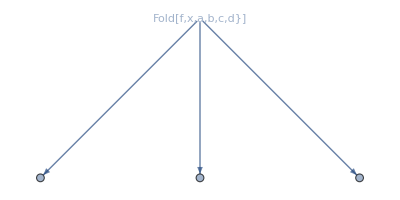

```mathematica
Graph[{"Fold[f,x,a,b,c,d}]",Fold[{f,x,a,b,c,d}],Fold[f,{x,a,b,c,d}],Fold[f,x,{a,b,c,d}]},{"Fold[f,x,a,b,c,d}]"->Fold[{f,x,a,b,c,d}],"Fold[f,x,a,b,c,d}]"->Fold[f,{x,a,b,c,d}],"Fold[f,x,a,b,c,d}]"->Fold[f,x,{a,b,c,d}]},VertexShapeFunction->{"Fold[f,x,a,b,c,d}]"->(Inset[Framed["Fold[f,x,a,b,c,d}]"],#]&)}]
```

```mathematica
VertexShapeFunction->{"Fold[f,x,a,b,c,d}]"->(Inset[Framed["Fold[f,x,a,b,c,d}]"],#]&)}(*check options of Framed*)
```

#### Example for Poster Session

```mathematica
input="Fold[f,x,{a,b,c}]";
dropped=StringDrop[input,{#}]&/@Range[StringLength[input]];
filtered=Select[dropped,Not[messageAnalysis[#]]&];
corrected=syntaxCorrectorWithoutNotation[#,True,20]&/@filtered;
filtocor=Thread[filtered[[#]]->corrected[[#]]]&/@Range[Length[filtered]];
intofil=Thread[input->filtered];
```

```mathematica
Column[input]->Column[filtered]->TableForm[corrected]
```

Column[Fold[f,x,{a,b,c}]]→Foldf,x,{a,b,c}]
Fold[f,x,a,b,c}]
Fold[f,x,{a,b,c]
Fold[f,x,{a,b,c}→F[oldf,x,{a,b,c}] | Fo[ldf,x,{a,b,c}] | Fol[df,x,{a,b,c}] | Fold[f,x,{a,b,c}] | Foldf[,x,{a,b,c}] | 
Fold[{f,x,a,b,c}] | Fold[f{,x,a,b,c}] | Fold[f,{x,a,b,c}] | Fold[f,x{,a,b,c}] | Fold[f,x,{a,b,c}] | Fold[f,x,a{,b,c}]
Fold[f,x,{a,b,}c] | Fold[f,x,{a,b,c}] |  |  |  | 
Fold[f,x,{a,b,c}] |  |  |  |  |

```mathematica
graph=Rasterize[Graph[Flatten@{intofil,filtocor},GraphLayout->"SpringEmbedding",VertexLabels->Placed["Name",Above],VertexLabelStyle->Directive[FontSize->18,Background->White],ImageSize->600],RasterSize->1000,ImageSize->400]
```

-Graphics-

```mathematica
graph=Rasterize[Graph[Flatten@{intofil,filtocor},GraphLayout->"BalloonEmbedding",VertexLabels->Placed["Name",Above],VertexLabelStyle->Directive[FontSize->17,Background->White],ImageSize->600],RasterSize->1000]
```

-Graphics-

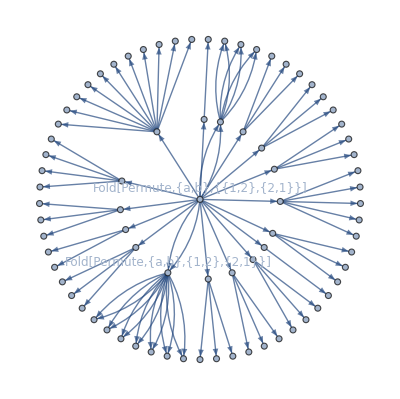

```mathematica
graph=Graph[Flatten@{intofil,filtocor},VertexLabels->{
"Fold[Permute,{a,b},{{1,2},{2,1}}]"->Placed[Style["Fold[Permute,{a,b},{{1,2},{2,1}}]",FontFamily->"Times New Roman",FontSize->12,Background->White],Above],
"Fold[Permute,{a,b},{1,2},{2,1}}]"->Placed[Style["Fold[Permute,{a,b},{1,2},{2,1}}]",FontFamily->"Times New Roman",FontSize->12,Background->White],Above]
},GraphLayout->"RadialEmbedding"]
```

```mathematica
img1=Rasterize[graph,RasterSize->1000]
```

-Graphics-

```mathematica
ImageDimensions[img1]
```

{360,359}

```mathematica
img2=Graphics[{EdgeForm[{Black,Thickness[0.001]}],
Blue,Opacity[0.25],Disk[{180,180},40],
Red,Opacity[0.25],Disk[{180,180},90],
Green,Opacity[0.25],Disk[{180,180},175]
}];
Show[img1,img2]
```

-Graphics-

```mathematica
img2=Graphics[{EdgeForm[{Black,Thickness[0.01]}],Red,Opacity[0.25],Disk[{50,50},10]}];
```

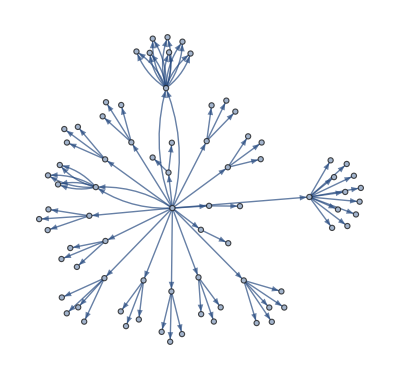

```mathematica
Graph[Flatten@{intofil,filtocor},VertexLabels->Placed["Name",Tooltip]]
```

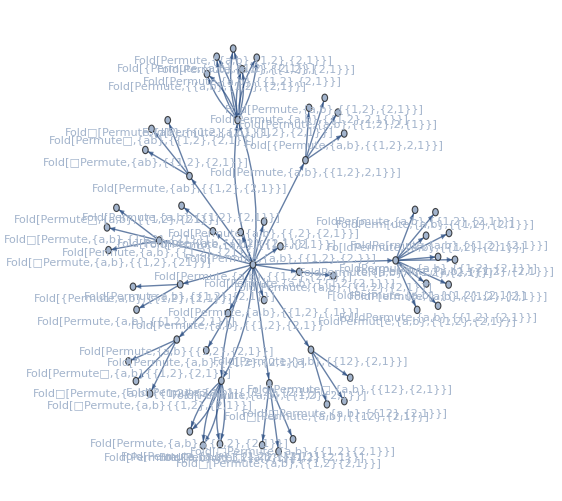

```mathematica
Graph[Flatten@{intofil,filtocor},VertexLabels->Placed["Name",Below]]
```

## ...

```mathematica
ss=Table[StringInsert["N[N[Nest[Nest[x^2,x,6,4,3]]]","□",i],{i,1,StringLength["N[N[Nest[Nest[x^2,x,6,4,3]]]"]+1}]
```

{□N[N[Nest[Nest[x^2,x,6,4,3]]],N□[N[Nest[Nest[x^2,x,6,4,3]]],N[□N[Nest[Nest[x^2,x,6,4,3]]],N[N□[Nest[Nest[x^2,x,6,4,3]]],N[N[□Nest[Nest[x^2,x,6,4,3]]],N[N[N□est[Nest[x^2,x,6,4,3]]],N[N[Ne□st[Nest[x^2,x,6,4,3]]],N[N[Nes□t[Nest[x^2,x,6,4,3]]],N[N[Nest□[Nest[x^2,x,6,4,3]]],N[N[Nest[□Nest[x^2,x,6,4,3]]],N[N[Nest[N□est[x^2,x,6,4,3]]],N[N[Nest[Ne□st[x^2,x,6,4,3]]],N[N[Nest[Nes□t[x^2,x,6,4,3]]],N[N[Nest[Nest□[x^2,x,6,4,3]]],N[N[Nest[Nest[□x^2,x,6,4,3]]],N[N[Nest[Nest[x□^2,x,6,4,3]]],N[N[Nest[Nest[x^□2,x,6,4,3]]],N[N[Nest[Nest[x^2□,x,6,4,3]]],N[N[Nest[Nest[x^2,□x,6,4,3]]],N[N[Nest[Nest[x^2,x□,6,4,3]]],N[N[Nest[Nest[x^2,x,□6,4,3]]],N[N[Nest[Nest[x^2,x,6□,4,3]]],N[N[Nest[Nest[x^2,x,6,□4,3]]],N[N[Nest[Nest[x^2,x,6,4□,3]]],N[N[Nest[Nest[x^2,x,6,4,□3]]],N[N[Nest[Nest[x^2,x,6,4,3□]]],N[N[Nest[Nest[x^2,x,6,4,3]□]],N[N[Nest[Nest[x^2,x,6,4,3]]□],N[N[Nest[Nest[x^2,x,6,4,3]]]□}

```mathematica
s3=Riffle[StringSplit[str,s2],Style[#,Red]&/@s2];
s4=TextCell[Row[s3]];
```

```mathematica
EvaluationNotebook[]
```

sr7a8_shm16FrontEndObject[LinkObject["sr7a8_shm", 3, 1]]16FinalVersion.nbC:\Users\Andrey.Krotkih\Documents\GitHub\WSS2017\FinalVersion.nb

```mathematica
,
Dynamic[Quiet[ToExpression[$x]]]
```

```mathematica
syntaxCorrector["f[",False,20]
```

Closing bracket missing
f[]

```mathematica
s1
```

{{1,]f[},{2,f][},{3,f[]}}

```mathematica
s2
```

{}

```mathematica
testAnalyser[s1[[3,2]],True]
```

True

```mathematica
Clear["Global`*"]
```

```mathematica
s1
```

{{1,□}}

```mathematica
s2
```

{}

```mathematica
syntaxCorrector["F[ccccv",True,20]
```

Closing bracket missing
F[]ccccv
F[c]cccv
F[cc]ccv
F[ccc]cv
F[cccc]v
F[ccccv]

```mathematica
s1
```

{{1,]F[ccccv},{2,F][ccccv},{3,F[]ccccv},{4,F[c]cccv},{5,F[cc]ccv},{6,F[ccc]cv},{7,F[cccc]v},{8,F[ccccv]}}

```mathematica
s2
```

{{3,F[]ccccv},{4,F[c]cccv},{5,F[cc]ccv},{6,F[ccc]cv},{7,F[cccc]v}}

```mathematica
messagePrinter["Nest[f,x,]"]
```

{Nest::intnm}

```mathematica
$MessageList
```

```mathematica
"{{1,2},{a,b,c}"->"{{1,2},{a,b,c}}"
```

```mathematica
"{{1,2},{a,b,c}"->"AASTriangle[...]"
```

```mathematica
"{{1,2},{a,b,c}}"
```

```mathematica
"{{3,2},{a,b,c}}"->"{{1,2},{a,b,c}}"
```

1) NN: dataset, and architecture
2) Applications
3) reading cells

A)
1) Adapting the pair of expressions for the NN.
2) We construct the neural net as follows

```mathematica
"{{_,_},{_,_,_}"->"{{_,_},{_},_,_}"
```

3) The main program should be as follows

```mathematica
input:"{{1,2},{a,b,c}"->convertedInput:"{{_,_},{_,_,_}"->resultingNN:"{{_,_},{_},_,_}"->"{{1,2},{a},b,c}"
```

B) OR we can try to have a better architecture for the neural net or better examples.

```mathematica
StringReplace["{{1,2},{a,b,c,de}}",LetterCharacter:>"_"]
```

{{1,2},{_,_,_,__}}

```mathematica
StringReplace["{{1,2},{a,b,c,de}}",x:LetterCharacter../;Not@MemberQ[Names["System`*"],x]:>"_"]
```

{{1,2},{_,_,_,_}}

```mathematica
StringReplace["Fold[f,{1,2}]",x:LetterCharacter../;MemberQ[Names["System`*"],Echo@x]:>"_"]
```

Fold

f

_[f,{1,2}]

```mathematica
ToString[Fold]<>"["<>ToString[SyntaxInformation[Fold][[1,2]]]<>"]"
```

Fold[{_, _., _.}]

```mathematica
.
```

```mathematica
StringReplace["Fold[f,{1,2}]",LetterCharacter:>"_"]
```

____[_,{1,2}]

```mathematica
ToCharacterCode["{{3,2},{a,b,c}}"]
```

{123,123,51,44,50,125,44,123,97,44,98,44,99,125,125}

```mathematica
ToCharacterCode["{{1,2},{a,b,c}}"]
```

{123,123,49,44,50,125,44,123,97,44,98,44,99,125,125}

```mathematica
If[ListQ[result],(*display message*),...]
```

```mathematica
ClearAll[Fbold]
```

```mathematica
Options[InputField]
```

{Alignment→{Automatic,Automatic},Appearance→Automatic,Background→Automatic,BaselinePosition→Automatic,BaseStyle→{},ContentPadding→True,ContinuousAction→False,DefaultBaseStyle→InputField,DefaultFieldHintStyle→FieldHintStyle,Enabled→Automatic,FieldCompletionFunction→Automatic,FieldHint→Null,FieldHintStyle→{},FieldMasked→False,FieldSize→Automatic,FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→Automatic,MenuList→{},Method→{}}

```mathematica
strspl=StringSplit["Nest[f,x,4]",x:PunctuationCharacter:>x]
```

{Nest,[,f,,,x,,,4,]}

```mathematica
correctSplitting[str_String]:=
Module[{s=str,s1,s2,result={},i},
s1=StringSplit[str,x:PunctuationCharacter:>x];
For[
i=1,i≤Length[s1],i++,
If[
Not[MemberQ[Names["System`*"],s1[[i]]]],
s2=StringDrop[s1[[i]],{#}]&/@Range[StringLength[s1[[i]]]];
AppendTo[result,{s1[[1;;i-1]],s2[[#]],s1[[i+1;;]]}&/@Range[StringLength[s1[[i]]]]]
]
];
StringJoin/@Flatten[result,1]
]
```

```mathematica
correctInserting[str_String,strinst_String]:=
Module[{s=str,s1,s2,result={},i,symb=strinst},
s1=StringSplit[str,x:PunctuationCharacter:>x];
For[
i=1,i≤Length[s1],i++,
If[
Not[MemberQ[Names["System`*"],s1[[i]]]],
s2={#+Total[StringLength[#]&/@(s1[[1;;i-1]])],StringInsert[s1[[i]],symb,{#}]}&/@Range[StringLength[s1[[i]]]];
AppendTo[result,{s2[[#,1]],{s1[[1;;i-1]],s2[[#,2]],s1[[i+1;;]]}}&/@Range[StringLength[s1[[i]]]]]
]
];
(*StringJoin/@Flatten[result,1]*)
Transpose[{Transpose[Flatten[result,1]][[1]],
StringJoin/@Transpose[Flatten[result,1]][[2]]}]
]
```

```mathematica
correctInserting["Nestfhh,x,4]","["]
```

{{1,[Nestfhh,x,4]},{2,N[estfhh,x,4]},{3,Ne[stfhh,x,4]},{4,Nes[tfhh,x,4]},{5,Nest[fhh,x,4]},{6,Nestf[hh,x,4]},{7,Nestfh[h,x,4]},{8,Nestfhh[,x,4]},{9,Nestfhh,[x,4]},{10,Nestfhh,x[,4]},{11,Nestfhh,x,[4]},{12,Nestfhh,x,4[]}}

```mathematica
Transpose[Flatten[correctInserting["Nestfhh,x,4]","["],1]][[1]]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
StringJoin/@Transpose[Flatten[correctInserting["Nestfhh,x,4]","["],1]][[2]]
```

{[Nestfhh,x,4],N[estfhh,x,4],Ne[stfhh,x,4],Nes[tfhh,x,4],Nest[fhh,x,4],Nestf[hh,x,4],Nestfh[h,x,4],Nestfhh[,x,4],Nestfhh,[x,4],Nestfhh,x[,4],Nestfhh,x,[4],Nestfhh,x,4[]}

```mathematica
StringJoin/@Flatten[correctInserting["Nestfhh,x,4]","["],1]
```

{[Nestfhh,x,4],N[estfhh,x,4],Ne[stfhh,x,4],Nes[tfhh,x,4],Nest[fhh,x,4],Nestf[hh,x,4],Nestfh[h,x,4],Nestfhh[,x,4],Nestfhh,[x,4],Nestfhh,x[,4],Nestfhh,x,[4],Nestfhh,x,4[]}

```mathematica
correctSplitting["Nest[fhh,x,4]"]
```

{Nestfhh,x,4],Nest[hh,x,4],Nest[fh,x,4],Nest[fh,x,4],Nest[fhhx,4],Nest[fhh,,4],Nest[fhh,x4],Nest[fhh,x,],Nest[fhh,x,4}

```mathematica
StringJoin/@Flatten[correctSplitting["Nest[fhh,x,4]"],1]
```

{Nestfhh,x,4],Nest[hh,x,4],Nest[fh,x,4],Nest[fh,x,4],Nest[fhhx,4],Nest[fhh,,4],Nest[fhh,x4],Nest[fhh,x,],Nest[fhh,x,4}

```mathematica
Flatten[Flatten[correctSplitting["Nest[f,x,4]"],1][[2]]]
```

{Nest,[,,,,x,,,4,]}